# Feature extractor with images ranged between 0.2 to 10 Miles

## Neural net initilization

```mathematica
ClearAll["Global`*"]
```

```mathematica
ClearAll[tnet]
tnet = Import[File["/Users/mehmetsahin/Downloads/2017-12-27T18-42-44_0_0123_05898_3.71e-3_9.47e-2.wlnet"]]
```

NetChain[<>]

```mathematica
choppedTNet = NetTake[tnet,1]
```

NetChain[<>]

## Functions

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
ClearAll[fromFileNameGetGeoRange,fileLocation]

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];

fileLocation[folderName_, hash_] := 
	FileNameJoin[{NotebookDirectory[],"features",folderName,IntegerString[Hash[hash], 36]<>".wxf"}]
```

```mathematica
getFileNames["validation"]//Length
```

```mathematica
ClearAll[getFileNames]
getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

getwxfFileNames[folderName_] := 
	FileNames["*.wxf",FileNameJoin[{NotebookDirectory[],"features",folderName}],Infinity];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_List] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		fileNames
	]
```

```mathematica
binaryWrite[expr_]:=binaryWrite[expr,CreateFile[]];
binaryWrite[expr_,file_]:=With[{bytes=BinaryWrite[file,BinarySerialize[expr]]},Close[file];
bytes];
binaryRead[file_]:=BinaryDeserialize[ReadByteArray[file]];
```

```mathematica
getFileNames["training"][[1]]
```

/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/training/ODpBAy1TBVBvaW50ZgJzBExpc3Ry01C6eRvvPUBym~t0Ps7ZV8AtUwRab29tcgbEcAYDiMQ~LVMIR2VvUmFuZ2VyiFZ9gdBZ~D8=/ODpBAi1TCEdlb1JhbmdlcohWfYHQWew~LVMGTnVtYmVyQwE=.png

```mathematica
fileLocation["training","asda"]
```

/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/features/training/1n7spk599ajwb.wxf

```mathematica
ClearAll[storeTheFeatures]

storeTheFeatures[folderName_String,batchSize_:1000] := 
	storeTheFeatures[folderName, associateFilesToGeoRange[getFileNames[folderName]],batchSize]

storeTheFeatures[folderName_String, dataFiles_List, batchSize_] := 
	DynamicModule[
		{filename, print = "Starting job"},
		PrintTemporary[Dynamic[print]];
		MapIndexed[
			Function[
				{partitionedDataFiles, index},
				filename = fileLocation[folderName, Keys[partitionedDataFiles]];
				If[
					Not @ FileExistsQ @ filename,
					binaryWrite[
						Thread[
							choppedTNet[Keys[partitionedDataFiles]] -> Values[partitionedDataFiles]
						], 
						filename
					];
					print = StringJoin[{"Part ", index, " of ", Length[dataFiles] / batchSize, " is Done"}    /. s:Except[_String] :> ToString[s]]
				]
			],
			Partition[dataFiles, batchSize]
		]	
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

### Export the data:

validation features:

```mathematica
storeTheFeatures["validation",350];
```

training features:

```mathematica
storeTheFeatures["training",1149];
```

testing features:

```mathematica
storeTheFeatures["testing",350];
```

### Import the data:

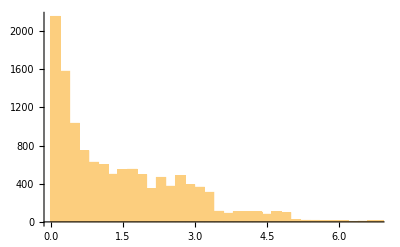

```mathematica
associateFilesToGeoRange[getFileNames["training"]][[All,2]]//Histogram
```

```mathematica
trainFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["training"]]];
validationFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["validation"]]];
testFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["testing"]]];
```

```mathematica
trainFeatures//Length
testFeatures//Length
```

12639

1050

## Train the last layer with ConvolutionLayer 16 and join the net chains: Done

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[16,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[128],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeatures,ValidationSet->validationFeatures]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test:

```mathematica
test = RandomSample@associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
test[[All,2]]//MinMax
```

{0.0666667,10.}

```mathematica
train = (RandomSample@associateFilesToGeoRange[getFileNames["training"]]);
```

```mathematica
min =95;
max=100;
test[[min;;max]]
Map[Import,test[[min;;max,1]]]
newTrainedNet[Map[Import,test[[min;;max,1]]]]
```

{File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RycNtcmeIYPkBytFUD+mzKV8AtUwRab29tcjpNGx53O+o~LVMIR2VvUmFuZ2VygFIKXJ93IEA=/ODpBAi1TCEdlb1JhbmdlcgBuuHrU9AVALVMGTnVtYmVyQwc=.png]→2.74455,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Rydxhnp~zbPUByonh5tAbkV8AtUwRab29tcurYOFCL76c~LVMIR2VvUmFuZ2Vy3ARWVIUP5T8=/ODpBAi1TCEdlb1JhbmdlcnoGyMWxFMw~LVMGTnVtYmVyQwE=.png]→0.219382,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyjCiAd1ruPUBySZ9diAHUV8AtUwRab29tcspkbY~pN70~LVMIR2VvUmFuZ2VyIjSmdKUY9T8=/ODpBAi1TCEdlb1JhbmdlcoJFiJvcINw~LVMGTnVtYmVyQwc=.png]→0.439506,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyRmMdiJScPUByaxfZnarIV8AtUwRab29tcqX2gXGJCeU~LVMIR2VvUmFuZ2VyWAEMKxWSGkA=/ODpBAi1TCEdlb1JhbmdlcjpWXce4tgFALVMGTnVtYmVyQwM=.png]→2.21422,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ry3fhYu4vaPUByBssAfrXUV8AtUwRab29tcgn0P7p87bo~LVMIR2VvUmFuZ2VyecXg~nWx8z8=/ODpBAi1TCEdlb1JhbmdlcvaxK6nyQdo~LVMGTnVtYmVyQwM=.png]→0.410275,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyM1JN0slrQEByUgESHDshWMAtUwRab29tcgy91bFxoLY~LVMIR2VvUmFuZ2Vy~rYfcBIP8T8=/ODpBAi1TCEdlb1JhbmdlclJJKkDDvtY~LVMGTnVtYmVyQwY=.png]→0.355393}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{3.56836,0.176124,2.17557,1.18474,3.0884,1.99239}

Check the error on test data:

```mathematica
calculateError[newTrainedNet,test]
```

0.87168

```mathematica
calculateError[trainedTnet3,testFeatures]
```

1.01408

Check the error on training data:

```mathematica
calculateError[newTrainedNet,train]
```

0.565138

```mathematica
calculateError[trainedTnet3,trainFeatures]
```

0.652943

Both of this number should be the same!

```mathematica
calculateMeanSq[trainedTnet3,validationFeatures]
calculateMeanSq[trainedTnet3,trainFeatures]
```

0.716068

0.425762

## Train the last layer with ConvolutionLayer 64 and join the net chains: Have not trained

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[64,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[512],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeatures,ValidationSet->validationFeatures]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test:

```mathematica
ClearAll[test];
test = RandomSample@associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
test[[All,2]]//MinMax
```

{0.0666667,10.}

```mathematica
train = (RandomSample@associateFilesToGeoRange[getFileNames["training"]]);
```

```mathematica
min =80;
max=85;
test[[min;;max]]//Column
Map[Import,test[[min;;max,1]]]
newTrainedNet[Map[Import,test[[min;;max,1]]]]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RypLg5IiqhPUByCtEHnS~fV8AtUwRab29tcpFZCX6OduY~LVMIR2VvUmFuZ2VyuQ1lWjtRHEA=/ODpBAi1TCEdlb1JhbmdlcnteQzzS4AJALVMGTnVtYmVyQwU=.png]→2.35978
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ryd0VbVob7PUBy~l20QCTkV8AtUwRab29tcgypODl+pdM~LVMIR2VvUmFuZ2VyfDWyn7qqCUA=/ODpBAi1TCEdlb1Jhbmdlcnw1sp+6qvk~LVMGTnVtYmVyQwQ=.png]→1.60418
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyHMgF4QH8PUByii37j4LVV8AtUwRab29tcspkbY~pN90~LVMIR2VvUmFuZ2VyvM0~Dj+yEkA=/ODpBAi1TCEdlb1JhbmdlcrzNPw4~sgJALVMGTnVtYmVyQwI=.png]→2.33703
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyRp+FbTr9REBysn8u3zf0VcAtUwRab29tcgn0P7p87do~LVMIR2VvUmFuZ2VyE196mA9LEUA=/ODpBAi1TCEdlb1JhbmdlchNfepgPSwFALVMGTnVtYmVyQwQ=.png]→2.16165
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyjJBdCjJfQEBynHHNfZEqWMAtUwRab29tcrB0EOh~dOk~LVMIR2VvUmFuZ2VyWPXgFYP7H0A=/ODpBAi1TCEdlb1JhbmdlcjpO62NXUgVALVMGTnVtYmVyQwc=.png]→2.66521
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyonMC2cJfQEByiu4J204vWMAtUwRab29tcvEUELpl4NA~LVMIR2VvUmFuZ2VyDoAgNxZGBkA=/ODpBAi1TCEdlb1Jhbmdlcr2qgEnIsu0~LVMGTnVtYmVyQwQ=.png]→0.928074

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{2.57042,1.48601,1.54825,2.60598,2.90062,1.0579}

Check the error on test data:

```mathematica
calculateError[trainedTnet3,testFeatures]
```

0.74318

Check the error on training data:

```mathematica
calculateError[trainedTnet3,trainFeatures]
```

0.502429

Both of this number should be the same!

```mathematica
calculateMeanSq[trainedTnet3,validationFeatures]
calculateMeanSq[trainedTnet3,trainFeatures]
```

0.752029

0.46958

## Train the last layer with PoolingLayer 8 and join them: Done

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[1000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar","Input"->{512,8,8}]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeatures,ValidationSet->validationFeatures]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

```mathematica
train = (RandomSample@associateFilesToGeoRange[getFileNames["training"]]);
```

```mathematica
train[[All,2]]//MinMax
```

{0.0666667,10.}

```mathematica
calculateError[newTrainedNet,train]
```

1.02859

### Test:

```mathematica
test = RandomSample@associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
test[[All,2]]//MinMax
```

{0.0666667,10.}

```mathematica
min =100;
max=105;
test[[min;;max]]
Map[Import,test[[min;;max,1]]]
newTrainedNet[Map[Import,test[[min;;max,1]]]]
```

{File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ryj0oaSqC+PUByhzFaKg7iV8AtUwRab29tcnT2amQ~de0~LVMIR2VvUmFuZ2VyWh0bB2pxIkA=/ODpBAi1TCEdlb1JhbmdlclodGwdqcSJALVMGTnVtYmVyQwE=.png]→9.22151,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ry3fhYu4vaPUByBssAfrXUV8AtUwRab29tcgn0P7p87bo~LVMIR2VvUmFuZ2VyecXg~nWx8z8=/ODpBAi1TCEdlb1JhbmdlcnnF4P51seM~LVMGTnVtYmVyQwE=.png]→0.615413,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ryx0ShQZfTPUByiGZiqfbbV8AtUwRab29tcojyh1EsS84~LVMIR2VvUmFuZ2VyJ968vqQnBEA=/ODpBAi1TCEdlb1Jhbmdlcol9plOG3+o~LVMGTnVtYmVyQwQ=.png]→0.839786,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ry7ZkeDsJ0QEByKpUs34w0WMAtUwRab29tcnZprNYks7I~LVMIR2VvUmFuZ2Vy~s0suqZO7T8=/ODpBAi1TCEdlb1Jhbmdlcv7NLLqmTu0~LVMGTnVtYmVyQwE=.png]→0.915851,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyPfDSf7UBPkByAZvs9PzIV8AtUwRab29tch68YnD~utg~LVMIR2VvUmFuZ2VyDMBFgxLlD0A=/ODpBAi1TCEdlb1JhbmdlcgzARYMS5f8~LVMGTnVtYmVyQwM=.png]→1.99343,File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyFytihELaREBy3ogOI4fqVcAtUwRab29tcuIskEVsBcs~LVMIR2VvUmFuZ2Vyfhs1hIUmAkA=/ODpBAi1TCEdlb1Jhbmdlcn4bNYSFJgJALVMGTnVtYmVyQwE=.png]→2.26881}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{5.09526,1.87652,1.17691,0.540592,1.65963,3.75213}

```mathematica
calculateError[newTrainedNet,test]
```

0.882892

```mathematica
calculateError[trainedTnet3,testFeatures]
```

0.74318

Check the error on training data:

```mathematica
calculateError[trainedTnet3,trainFeatures]
```

0.502429

Both of this number should be the same!

```mathematica
calculateMeanSq[trainedTnet3,validationFeatures]
calculateMeanSq[trainedTnet3,trainFeatures]
```

0.752029

0.46958

## Change the last layer and train again: Done

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[8000],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeatures,ValidationSet->validationFeatures]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

```mathematica
calculateError[newTrainedNet,test]
```

1.10567

## Change the last layer and train once again: Done

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[4,"Function"->Mean],FlattenLayer[],LinearLayer[4000],ElementwiseLayer[Ramp],LinearLayer[500],ElementwiseLayer[Abs],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeatures,ValidationSet->validationFeatures]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

```mathematica
calculateError[newTrainedNet,test[[1;;10]]]
```

0.907292

```mathematica
min =1;
max=10;
test[[min;;max]]//Column
Map[Import,test[[min;;max,1]]]
newTrainedNet[Map[Import,test[[min;;max,1]]]]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyVfUteUKwPUByXOZseT7pV8AtUwRab29tcrb1DjAXJO8~LVMIR2VvUmFuZ2Vyf~bVM055I0A=/ODpBAi1TCEdlb1JhbmdlclTzx+8S9wlALVMGTnVtYmVyQwY=.png]→3.24564
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyrLA~DZvAPUByidl+UKvTV8AtUwRab29tcm143O1ICsE~LVMIR2VvUmFuZ2VyU+D6vP8S+D8=/ODpBAi1TCEdlb1JhbmdlcoyV~H2qDOA~LVMGTnVtYmVyQwY=.png]→0.501546
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3Ry0tCnke~PPUBynXXdilfUV8AtUwRab29tcqT2gXGJCcU~LVMIR2VvUmFuZ2VyvGdykXv4~D8=/ODpBAi1TCEdlb1JhbmdlcrxncpF7+Ow~LVMGTnVtYmVyQwI=.png]→0.905332
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyMxQoa4b1REBy1yayiL~yVcAtUwRab29tctlPXdWDV+Q~LVMIR2VvUmFuZ2VyBLX4fgG4GUA=/ODpBAi1TCEdlb1JhbmdlcgLOpVRWJQFALVMGTnVtYmVyQwM=.png]→2.14323
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyZh1TqsTkREByZrtbb33xVcAtUwRab29tcgAAAAAAAPA~LVMIR2VvUmFuZ2VyAAAAAAAAJEA=/ODpBAi1TCEdlb1JhbmdlcqqqqqqqqgpALVMGTnVtYmVyQwE=.png]→3.33333
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyMxQoa4b1REBy1yayiL~yVcAtUwRab29tctlPXdWDV+Q~LVMIR2VvUmFuZ2VyBLX4fgG4GUA=/ODpBAi1TCEdlb1JhbmdlcgLOpVRWJQFALVMGTnVtYmVyQwg=.png]→2.14323
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyFAYrZjlVQEBytWR90mA7WMAtUwRab29tchSGa6lmU6I~LVMIR2VvUmFuZ2VyutuRFOKf4T8=/ODpBAi1TCEdlb1JhbmdlcrrbkRTin9E~LVMGTnVtYmVyQwM=.png]→0.275383
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyWJMzxrhoQEBy7UhA5noiWMAtUwRab29tcojyh1EsS44~LVMIR2VvUmFuZ2VyFG9eX9IT1j8=/ODpBAi1TCEdlb1JhbmdlchRvXl~SE8Y~LVMGTnVtYmVyQwI=.png]→0.17248
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RymmW5kL6qPUBy7WN7wYnVV8AtUwRab29tco2kEP+MvuU~LVMIR2VvUmFuZ2VylMnaHtNvG0A=/ODpBAi1TCEdlb1JhbmdlcmKGPL+MSgJALVMGTnVtYmVyQwk=.png]→2.2864
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyM+ZKuWF+QEByFazUjYM0WMAtUwRab29tcnwyQs4ZZt4~LVMIR2VvUmFuZ2Vy7b67NFZrE0A=/ODpBAi1TCEdlb1JhbmdlcuZT+vBy5Pk~LVMGTnVtYmVyQwg=.png]→1.61827

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{3.78665,0.381279,1.43917,1.23014,4.27285,2.22266,0.374842,1.05403,3.02117,1.54322}

## Import data from 0 to 4: Done

```mathematica
validationFeaturesSmall = TakeSmallestBy[validationFeatures,Last,UpTo[1975]];
trainFeaturesSmall = TakeSmallestBy[trainFeatures,Last,UpTo[11850]];
```

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{PoolingLayer[8,"Function"->Mean],FlattenLayer[],LinearLayer[512],ElementwiseLayer[Ramp],LinearLayer[1],ElementwiseLayer[Abs]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeaturesSmall,ValidationSet->validationFeaturesSmall]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test;

```mathematica
test = RandomSample@associateFilesToGeoRange[getFileNames["testing"]];
```

```mathematica
testSmall = TakeSmallestBy[test,Last,UpTo[990]];
```

```mathematica
calculateError[newTrainedNet,testSmall]
```

0.802853

```mathematica
min =950;
max=955;
testSmall[[min;;max]]//Column
Map[Import,testSmall[[min;;max,1]]]
newTrainedNet[Map[Import,testSmall[[min;;max,1]]]]
```

File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyRmMdiJScPUByaxfZnarIV8AtUwRab29tcqX2gXGJCeU~LVMIR2VvUmFuZ2VyWAEMKxWSGkA=/ODpBAi1TCEdlb1JhbmdlclgBDCsVkgpALVMGTnVtYmVyQwI=.png]→3.32133
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyRmMdiJScPUByaxfZnarIV8AtUwRab29tcqX2gXGJCeU~LVMIR2VvUmFuZ2VyWAEMKxWSGkA=/ODpBAi1TCEdlb1JhbmdlclgBDCsVkgpALVMGTnVtYmVyQwQ=.png]→3.32133
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyRmMdiJScPUByaxfZnarIV8AtUwRab29tcqX2gXGJCeU~LVMIR2VvUmFuZ2VyWAEMKxWSGkA=/ODpBAi1TCEdlb1JhbmdlclgBDCsVkgpALVMGTnVtYmVyQwM=.png]→3.32133
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyZh1TqsTkREByZrtbb33xVcAtUwRab29tcgAAAAAAAPA~LVMIR2VvUmFuZ2VyAAAAAAAAJEA=/ODpBAi1TCEdlb1JhbmdlcqqqqqqqqgpALVMGTnVtYmVyQwQ=.png]→3.33333
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyZh1TqsTkREByZrtbb33xVcAtUwRab29tcgAAAAAAAPA~LVMIR2VvUmFuZ2VyAAAAAAAAJEA=/ODpBAi1TCEdlb1JhbmdlcqqqqqqqqgpALVMGTnVtYmVyQwM=.png]→3.33333
File[/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/testing/ODpBAy1TBVBvaW50ZgJzBExpc3RyZh1TqsTkREByZrtbb33xVcAtUwRab29tcgAAAAAAAPA~LVMIR2VvUmFuZ2VyAAAAAAAAJEA=/ODpBAi1TCEdlb1JhbmdlcqqqqqqqqgpALVMGTnVtYmVyQwk=.png]→3.33333

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{1.94379,1.84053,1.59944,2.92055,1.45663,2.7381}